0.0611324

0.11949

0.582564

0.00409383

10057975

10058.

{{S→InterpolatingFunction[{{0.,90.}},<>],U→InterpolatingFunction[{{0.,90.}},<>],M→InterpolatingFunction[{{0.,90.}},<>],A→InterpolatingFunction[{{0.,90.}},<>],d→InterpolatingFunction[{{0.,90.}},<>]}}

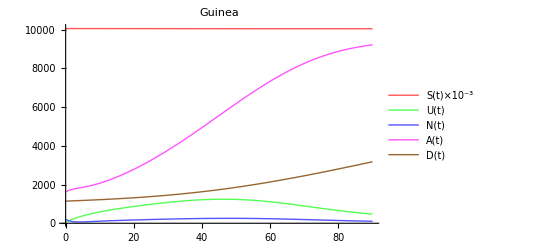

```mathematica
(* Ginea *)
ClearAll[n,d,A,M,S,U,p,q,a,x,Udata,Mdata,Adata,Ddata,Sdata];
x=0.0611324
p=0.11949
q=0.582564
a=0.00409383
n = 10057975
K = 0.001*n
eq= NDSolve[{U'[t]==(1-((M[t]+A[t])/K))*x/n*S[t]*(M[t]+A[t])-p*U[t],S'[t]==-(1-((M[t]+A[t])/K))*x/n*S[t]*(M[t]+A[t]),M'[t]==p*U[t]-q*M[t],A'[t]==q*M[t]-a*A[t],d'[t]==a*A[t],U[0]==58,M[0]==208,A[0]==1612,d[0]==1142,S[0]==10054955},{S,U,M,A,d},{t,0,90}]
SetOptions[Plot,BaseStyle->{FontSize->14}];

Plot[{(S[t]/(10^3)/.eq),(U[t]/.eq),(M[t]/.eq),(A[t]/.eq),(d[t]/.eq)},{t,0,90},PlotRange->All,PlotLegends->{"S(t)×10^-3","U(t)","N(t)","A(t)","D(t)"},PlotLabel->"Guinea",PlotStyle->{{Lighter[Red],Thick},{Lighter[Green],Thick},{Lighter[Blue],Thick},{Lighter[Magenta],Thick},{Brown,Thick}}]
```

```mathematica
"
```

0.00669021

0.00602125

0.00937902

0.00349354

3441790

6883.58

{{S→InterpolatingFunction[{{0.,90.}},<>],U→InterpolatingFunction[{{0.,90.}},<>],M→InterpolatingFunction[{{0.,90.}},<>],A→InterpolatingFunction[{{0.,90.}},<>],d→InterpolatingFunction[{{0.,90.}},<>]}}

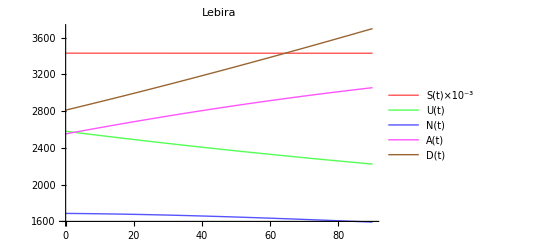

```mathematica
(* Lebira *)
ClearAll[K,n,d,A,M,S,U,p,q,a,x,Udata,Mdata,Adata,Ddata,Sdata];
x=0.00669021
p=0.00602125
q=0.00937902
a=0.00349354
n=3441790
K=0.002* n
eq= NDSolve[{U'[t]==(1-((M[t]+A[t])/K))*x/n*S[t]*(M[t]+A[t])-p*U[t],S'[t]==-(1-((M[t]+A[t])/K))*x/n*S[t]*(M[t]+A[t]),M'[t]==p*U[t]-q*M[t],A'[t]==q*M[t]-a*A[t],d'[t]==a*A[t],U[0]==2582,M[0]==1687,A[0]==2553,d[0]==2812,S[0]==3432156},{S,U,M,A,d},{t,0,90}]
Plot[{(S[t]/(10^3)/.eq),(U[t]/.eq),(M[t]/.eq),(A[t]/.eq),(d[t]/.eq)},{t,0,90},PlotRange->All,PlotLegends->{"S(t)×10^-3","U(t)","N(t)","A(t)","D(t)"},PlotLabel->"Lebira",PlotStyle->{{Lighter[Red],Thick},{Lighter[Green],Thick},{Lighter[Blue],Thick},{Lighter[Magenta],Thick},{Brown,Thick}}]
```

0.00378024

0.0223951

0.0547557

0.00360921

6440053

6440.05

{{S→InterpolatingFunction[{{0.,90.}},<>],U→InterpolatingFunction[{{0.,90.}},<>],M→InterpolatingFunction[{{0.,90.}},<>],A→InterpolatingFunction[{{0.,90.}},<>],d→InterpolatingFunction[{{0.,90.}},<>]}}

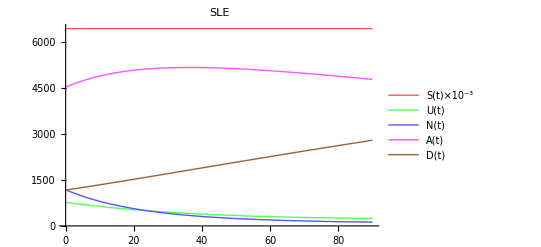

```mathematica
(* SLE *)
ClearAll[K,n,d,A,M,S,U,p,q,a,x,Udata,Mdata,Adata,Ddata,Sdata];
x=0.00378024
p=0.0223951
q=0.0547557
a=0.00360921
n=6440053
K=0.001* n
eq= NDSolve[{U'[t]==(1-((M[t]+A[t])/K))*x/n*S[t]*(M[t]+A[t])-p*U[t],S'[t]==-(1-((M[t]+A[t])/K))*x/n*S[t]*(M[t]+A[t]),M'[t]==p*U[t]-q*M[t],A'[t]==q*M[t]-a*A[t],d'[t]==a*A[t],U[0]==766,M[0]==1179,A[0]==4523,d[0]==1169,S[0]==6432416},{S,U,M,A,d},{t,0,90}]
(*For[i=0,i<87,i++,Print[N[(S[i]/.eq),7]]]*)
(*Plot[{(M[t]/.eq)},{t,0,75},PlotRange->All,PlotLegends->"--- N(t)"]
Plot[{(*U[t]/.eq,S[t]/.eq,M[t]/.eq,*)A[t]/.eq(*,d[t]/.eq*)},{t,0,90},PlotRange->All,PlotLegends->"Expressions"]
Plot[{(*U[t]/.eq,S[t]/.eq,M[t]/.eq,A[t]/.eq,*)d[t]/.eq},{t,0,90},PlotRange->All,PlotLegends->"Expressions"]
Plot[{(*(M[t]/.eq),*)(S[t]/.eq)},{t,0,90},PlotRange->All,PlotLegends->"Expressions"]
Plot[{(U[t]/.eq)},{t,0,90},PlotRange->All,PlotLegends->"Expressions"]
(*Plot[{(M[t]/.eq),(U[t]/.eq)},{t,0,90},PlotRange->All,PlotLegends->"Expressions"]*)*)

Plot[{(S[t]/(10^3)/.eq),(U[t]/.eq),(M[t]/.eq),(A[t]/.eq),(d[t]/.eq)},{t,0,90},PlotRange->All,PlotLegends->{"S(t)×10^-3","U(t)","N(t)","A(t)","D(t)"},PlotLabel->"SLE",PlotStyle->{{Lighter[Red],Thick},{Lighter[Green],Thick},{Lighter[Blue],Thick},{Lighter[Magenta],Thick},{Brown,Thick}}]
```